Get::noopen: Cannot open PolygonPlotMarkers`.

$Failed

PolygonMarker[All]

PolygonMarker[-Graphics-]

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

SetOptions::optnf: Joined is not a known option for Plot.

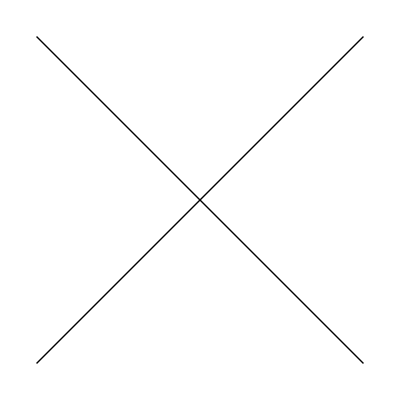
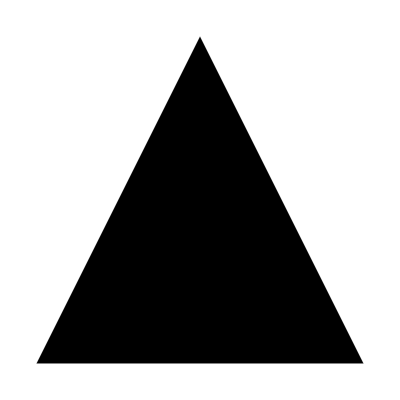
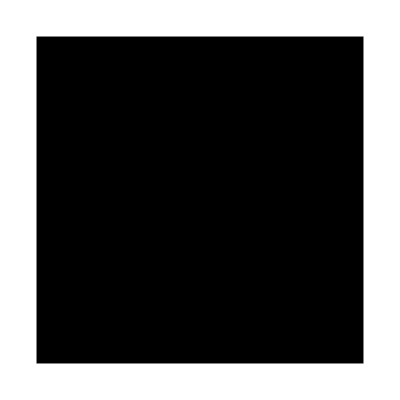
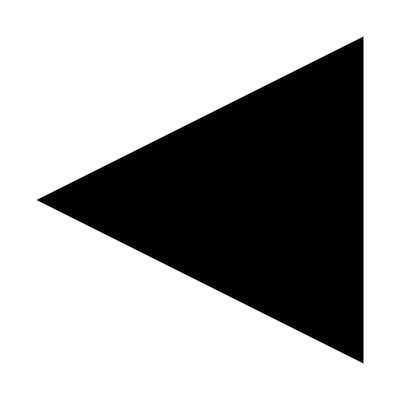
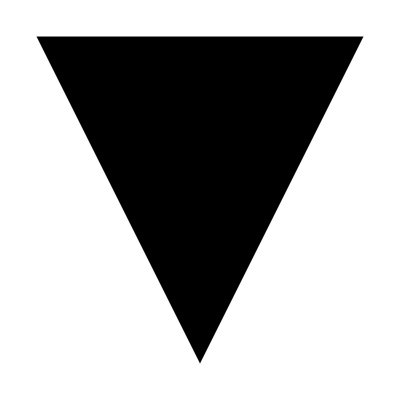
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373},\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
<<MaTeX`
<<PolygonPlotMarkers`

myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.002;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;

ts=0.02*{1,1/GoldenRatio};

fm[name_,size_:4]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes

fm[name_,size_:5]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

GetScaledLogTicks[min_,max_,scale_]:=Module[{ticks},ticks=#[Log[min],Log[max]]&/@{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]};
(*scale the tick length*)Table[{Exp[#[[1]]],#[[2]],scale*#[[3]]}&/@ticks[[i]],{i,2}]]

SetOptions[MaTeX,FontSize->fontSize]

SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black,Directive[Black,AbsoluteThickness[0.5]]],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[ListLogLogPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align,PlotRangePadding->0,ImagePadding->0]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
SetOptions[MaTeX,"Preamble"->{"\\usepackage[rgb,dvipsnames]{xcolor}","\\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373}","\\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392}","\\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882}","\\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}"}]
```

```mathematica
ticks={{Join[Table[{i,If[i<1,MaTeX[NumberForm[i,{4,1}]],""],ts},{i,0,1,.25}],Table[{i,"",0.5ts},{i,.125,1,.25}],{{0.975,Rotate[MaTeX["V_{ee}(x)"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<3,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,-4,4,1}],Table[{i,"",0.5ts},{i,-4.5,4,1}],{{2.75,MaTeX["x/a"],.0}}],{None}}}; 
Manipulate[pp1=Plot[V0*HeavisideTheta[b-Mod[x+b,a]],{x,-a*L,a*L},Filling->Bottom,FillingStyle->mygray,PlotStyle->{Thickness[.005],mygray},GridLines->None,Frame->True,FrameStyle->Black,ImageSize->{Automatic,5cm},FrameTicks->ticks,ImagePadding->{{25,2},{20,2}},PlotRange->{{-a*L,a*L},{0.0,1.1}},Axes->None],{{L,3},1,10,1},{{a,1},0,4},{{b,0.75},0,4},{{V0,0.25/0.75},0,10}]
```

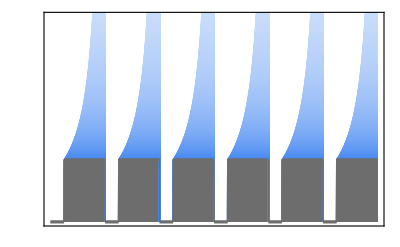

```mathematica
bs=Table[0.75-Sin[x],{x,0,π/4,π/4/500}];
pp1=Show[pp1,Table[Plot[0.25/bs[[bb]]*HeavisideTheta[bs[[bb]]-Mod[x+bs[[bb]],1]],{x,-3,3},Filling->Bottom,FillingStyle->Blend[{White,myblue},1-bb/Length[bs]],PlotStyle->None],{bb,Length[bs],1,-1}],pp1]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas.haller/mathematica_files

```mathematica
Export["kronig_penney_potential.png",pp1,ImageResolution->1200]
```

kronig_penney_potential.png

```mathematica
rr=221/101;
pts=ts;
ts=ts*rr;
ticks={{Join[Table[{i,If[i<1,MaTeX[NumberForm[i,{4,1}]],""],ts},{i,0,1,.25}],Table[{i,"",0.5ts},{i,.125,1,.25}],{{0.975,Rotate[MaTeX["V_{ee}(x)"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<2,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,-4,4,2}],Table[{i,"",0.5ts},{i,-5,4,2}],{{2.25,MaTeX["x/a"],.0}}],{None}}}; 
ts=pts;
Manipulate[pp2=Plot[V0(HeavisideTheta[b+Mod[x,a]]*HeavisideTheta[b-Mod[x,a]]),{x,-a*L,a*L},Filling->0,PlotStyle->mygray,FillingStyle->Opacity[.5],GridLines->None,Frame->True,FrameStyle->Black,ImageSize->{Automatic,5cm},AspectRatio->GoldenRatio,FrameTicks->ticks,ImagePadding->{{25,2},{20,2}},PlotRange->{{-a*L,a*L},{0.01,1.1}}],{{L,3},1,10,1},{{a,1},0,4},{{b,0.005},0,4},{{V0,100},1,100}]
```

```mathematica
mat={
{1,1,-1,-1},
{α,-α,-β,β},
{ⅇ^(ⅈ(α-k)*(a+b)),ⅇ^(-ⅈ(α+k)*(a+b)),-ⅇ^(ⅈ(β-k)*b),-ⅇ^(-ⅈ(β+k)*b)},
{(α-k)ⅇ^(ⅈ(α-k)*(a+b)),-(α+k)ⅇ^(-ⅈ(α+k)*(a+b)),-(β-k)ⅇ^(ⅈ(β-k)*b),(β+k)ⅇ^(-ⅈ(β+k)*b)}};
```

```mathematica
mat={
{1,1,-1,-1},
{α,-α,-β,β},
{ⅇ^(ⅈ(α-k)*(a-b)),ⅇ^(-ⅈ(α+k)*(a-b)),-ⅇ^(-ⅈ(β-k)*b),-ⅇ^(ⅈ(β+k)*b)},
{(α-k)ⅇ^(ⅈ(α-k)*(a-b)),-(α+k)ⅇ^(-ⅈ(α+k)*(a-b)),-(β-k)ⅇ^(-ⅈ(β-k)*b),(β+k)ⅇ^(ⅈ(β+k)*b)}};
```

```mathematica
(Det[mat]/.{b->-b}//FullSimplify)
```

ⅇ^(-ⅈ ((a+b) (k+α)+b (k+β))) ((-1+ⅇ^(2 ⅈ (a+b) α)) (-1+ⅇ^(2 ⅈ b β)) α^2-2 (1+ⅇ^(2 ⅈ (a+b) α)+ⅇ^(2 ⅈ b β)+ⅇ^(2 ⅈ ((a+b) α+b β))-2 ⅇ^(ⅈ (a (-k+α)+b (α+β)))-2 ⅇ^(ⅈ (a (k+α)+b (α+β)))) α β+(-1+ⅇ^(2 ⅈ (a+b) α)) (-1+ⅇ^(2 ⅈ b β)) β^2)

```mathematica
(2 α β (Cos[a k]-Cos[(a-b) α] Cos[b β])+(α^2+β^2) Sin[(a-b) α] Sin[b β])/.{b->-b}//FullSimplify
```

2 α β (Cos[a k]-Cos[(a+b) α] Cos[b β])-(α^2+β^2) Sin[(a+b) α] Sin[b β]

```mathematica
Clear[approx]
rhs[a_,b_,α_,β_]:=Cosh[(1+b/a)a α] Cos[b β]+(α^2+β^2)/(2 α β) Sinh[(1+b/a)a α] Sin[b β]
approx[a_,α_,P_]:=Cosh[α a]+P/(α a) Sinh[a α] 
appdata=Table[{√Abs[x],approx[1,√-x,0.5]},{x,0.001,100,.01}];
appdisp=Table[{ArcCos[approx[1,√-x,0.5]],√Abs[x]},{x,0.001,100,.01}];

Manipulate[
ListPlot[{appdisp,Table[{ArcCos[rhs[a,b,√-x,√(x-V0)]],√Abs[x]},{x,0.001,100,.01}]},PlotMarkers->False],{{a,1},0,10},{{b,1},0,10},{{V0,-1},-100,0}]

Manipulate[Show[

ListPlot[Table[{√Abs[x],rhs[a,b,√-x,√(x-V0)]},{x,0.001,100,.01}],PlotStyle->Black,Joined->True,PlotMarkers->False],
ListPlot[appdata,PlotStyle->Red,Joined->True,PlotMarkers->False]
]
,{{a,1},0,10},{{b,1},0,10},{{V0,-1},-100,0}]
```

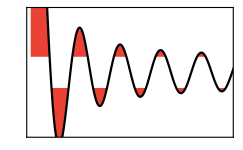

```mathematica
ticks={{Join[Table[{i,If[i<4,MaTeX[NumberForm[i,{4,1}]],""],ts},{i,-8,8,2}],Table[{i,"",0.5ts},{i,-7,8,2}],{{3.25,Rotate[MaTeX["f(\\alpha a)"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<30,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,0,50,5}],Table[{i,"",0.5ts},{i,2.5,50,5}],{{29,MaTeX["\\alpha a"],.0}}],{None}}}; 
pp2=Show[Plot[{Cos[x]+20.*Sin[x]/x,1,-1},{x,0,32},PlotStyle->None,Filling->{1->{3}},FillingStyle->{myred,Transparent},PlotRange->Full],Plot[{Cos[x]+20.*Sin[x]/x,1,-1},{x,0,32},PlotStyle->None,Filling->{1->{2}},FillingStyle->{Transparent,myred},PlotRange->Full],
Plot[{Cos[x]+20.*Sin[x]/x},{x,0,32},PlotStyle->Black],Frame->True,Axes->False,FrameStyle->Black,FrameTicks->ticks,ImageSize->8.6cm,PlotRange->{{0,30},4{-1,1}},PlotRangePadding->0]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["kronig_penney_transcendental.png",pp2,ImageResolution->1200]
```

/Users/andreas/Desktop

kronig_penney_transcendental.png

```mathematica
Manipulate[Plot[Cos[x]+pp*Sin[x]/x,{x,0,7}],{{pp,1.5},-10,10}]
```

```mathematica
Manipulate[Table[{ArcCos[approx[1,√-x,p]],√Abs[x]},{x,0.001,100,.01}]//ListPlot,{p,0,100}]
```

```mathematica
Clear[bands];
Clear[disp];
Clear[P];
allbands={};
Do[
flag=0;pflag=0;
kay=0;
shift=0;
sign=1;
ctr=0;
bands={};disp={};
Do[
flag=0;
val=Cos[√α]+P/(√α) Sin[√α];
If[Abs[val]^2≥1,flag=1;];

If[flag==0,
kay=(sign*ArcCos[val])/π+shift;
AppendTo[disp,{kay,α}];
];

If[flag==1&&pflag==0,
If[disp≠{},
AppendTo[bands,disp];
disp={};
sign*=-1;
If[sign<0,shift+=2];
];
];
pflag=flag;
 ,{α,0.001,200,0.1}];
AppendTo[allbands,bands];
,{P,{0.1,5,10,20}}]
```

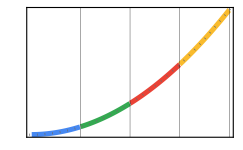

```mathematica
ticks={{Join[Table[{i,If[i<150,MaTeX[NumberForm[i,{4,1}]],""],ts},{i,0,200,25}],Table[{i,"",0.5ts},{i,12.5,200,25}],{{150,Rotate[MaTeX["E"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<4,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,0,8,1}],Table[{i,"",0.5ts},{i,.5,8,1}],{{3.75,MaTeX["k/\\pi"],.0}}],{None}}}; 
Show[ListPlot[allbands[[1]],PlotMarkers->None,PlotStyle->{Directive[myblue,Thickness[.015]],Directive[mygreen,Thickness[.015]],Directive[myred,Thickness[.015]],Directive[myyellow,Thickness[.015]]}],Plot[Evaluate[Table[(k π-2π*n)^2,{n,{0}}]],{k,-100,100
},PlotStyle->{mygray,Dotted}],ImageSize->8.6cm,FrameTicks->ticks,GridLines->{Table[i,{i,10}],{}},GridLinesStyle->Directive[Opacity[1],Black,Thickness[.001]]]
```

```mathematica
Clear[P];
Clear[bands];
Clear[disp];
Clear[allbands];
allbands={};
Do[
flag=0;pflag=0;
kay=0;
shift=0;
sign=1;
ctr=0;
bands={};disp={};
Do[
flag=0;
val=Cos[√α]+P/(√α) Sin[√α];
If[Abs[val]^2≥1,flag=1;];

If[flag==0,
kay=(sign*ArcCos[val])/π+shift;
AppendTo[disp,{kay,α}];
];

If[flag==1&&pflag==0,
If[disp≠{},
AppendTo[bands,disp];
disp={};
sign*=1;
If[sign<0,shift+=0];
];
];
pflag=flag;
 ,{α,0.001,200,0.0005}];
AppendTo[allbands,bands];
,{P,{0.1,1,5,20,50,1000}}]
```

```mathematica
ticks={{Join[Table[{i,If[i<150,MaTeX[NumberForm[i,{4,1}]],""],ts},{i,0,200,25}],Table[{i,"",0.5ts},{i,12.5,200,25}],{{150,Rotate[MaTeX["\\varepsilon"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<1,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,0,1,.25}],Table[{i,"",0.5ts},{i,.125,1,.25}],{{0.95,MaTeX["k/\\pi"],.0}}],{None}}}; 
tns=Thickness[.007];
Show[
Table[ListPlot[allbands[[ii]],PlotStyle->(colors={Directive[Blend[{White,myblue},1-(ii-1)/Length[allbands]],tns],Directive[Blend[{White,mygreen},1-(ii-1)/Length[allbands]],tns],Directive[Blend[{White,myred},1-(ii-1)/Length[allbands]],tns],Directive[Blend[{White,myyellow},1-(ii-1)/Length[allbands]],tns]})
,PlotMarkers->None,Joined->True
],{ii,Length[allbands],1,-1}]
,ImageSize->8.6cm/2,AspectRatio->1,FrameTicks->ticks,GridLines->None,PlotRange->{{0,1},{0,175}},PlotRangePadding->0]
```

-Graphics-

```mathematica
(Series[Sin[x]/x,{x,π,1}]==b//Normal)/.{x^2->y}//FullSimplify
```

b π+x==π

```mathematica
Series[P/x*Sin[x],{x,π,1}]//Normal//ExpandAll//FullSimplify
```

P-(P x)/π

```mathematica
Series[(π*P(1/P-1-Cos[x]))^2,{P,0,1}]//Normal
```

π^2-2 P π^2 (1+Cos[x])

```mathematica
Solve[(Series[Sin[x]/x,{x,π,3}]==b//Normal)/.{x^2->y},y]
```

{}

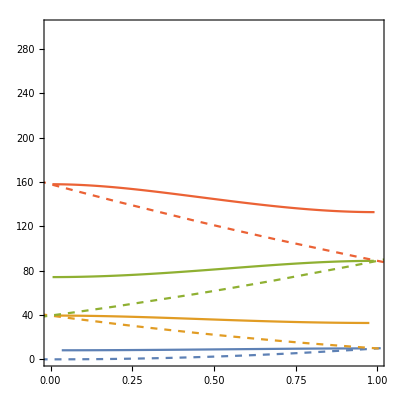

```mathematica
Show[ListPlot[bands,Joined->True,PlotRange->Full,PlotMarkers->None],Plot[Evaluate[Table[(k π-2π*n)^2,{n,{0,1,-1,2}}]],{k,-100,100
},PlotStyle->Dashed],AspectRatio->1,PlotRangePadding->0,PlotRange->{{0,1},{0,300}}]
```

0.05

Cos[3.06305 x]

Cos[0.0785398 x]

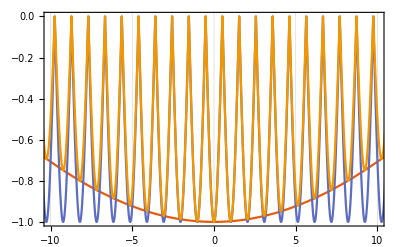

```mathematica
<<MaTeX`
k1=1;k2=.95;kp=k1+k2;km=k1-k2;kmin=Min[km,kp]
Cos[kp*x*(π/2)]
Cos[km*x*(π/2)]
Plot[Evaluate[-Abs[{%,%%,%*%%}]],{x,-1/kmin,1/kmin},GridLines->{Table[i,{i,-2/km,2/km,2/kp}],None},PlotTheme->"Scientific",FrameLabel->MaTeX[{"x/\\lambda_0","-|I|"}],PlotRange->{{-10,10},Automatic},MaxRecursion->20]
```

```mathematica
Series[SubMinus[k] Tan[SubMinus[k] x]+SubPlus[k] Tan[SubPlus[k] x],{SubMinus[k],0,2}]//Normal
```

x k_-^2+k_+ Tan[x k_+]

```mathematica
Solve[x SubMinus[k]^2+SubPlus[k] Tan[x SubPlus[k]]==0,x]
```

Solve[x k_-^2+k_+ Tan[x k_+]==0,x]

```mathematica
(x/.Table[FindRoot[km Tan[km x*π] -kp Tan[kp x*π]==0,{x,i}],{i,0,1/km,1/kp}])
```

{0.,0.527791,1.05567,1.58373,2.11215,2.6412,3.17149,3.70457,4.24651,5.,5.,5.75349,6.29543,6.82851,7.3588,7.88785,8.41627,8.94433,9.47221,10.}

```mathematica
Table[{i,i-x/.FindRoot[km Tan[km x*π] -kp Tan[kp x*π]==0,{x,i}]},{i,0,0.5/km,1/kp}]
```

{{0.,0.},{0.526316,-0.00147554},{1.05263,-0.00303611},{1.57895,-0.00478762},{2.10526,-0.00688971},{2.63158,-0.00962602},{3.15789,-0.0135929},{3.68421,-0.0203556},{4.21053,-0.035987},{4.73684,-0.263154}}

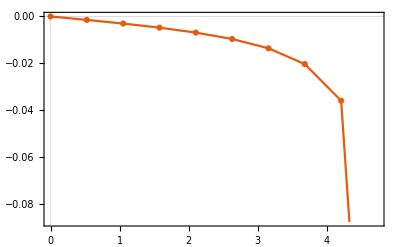

```mathematica
ListPlot[Table[{i,i-x/.FindRoot[km Tan[km x*π] -kp Tan[kp x*π]==0,{x,i}]},{i,0,0.5/km,1/kp}],PlotTheme->"Scientific",FrameLabel->{MaTeX["i"],MaTeX["u_i"]}]
```

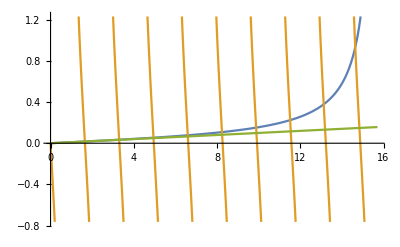

```mathematica
Plot[{km Tan[km x], -kp Tan[kp x],x km^2},{x,0,π/kmin/2}]
```

```mathematica
D[Cos[a*x]Cos[b*x],x]
```

-a Cos[b x] Sin[a x]-b Cos[a x] Sin[b x]

```mathematica
Solve[(-a Cos[b x] Sin[a x])/(b Cos[a x] Sin[b x])==1,x]
```

Solve[-(a Cot[b x] Tan[a x])/b==1,x]

```mathematica
Solve[D[Cos[a*x]Cos[b*x],x]==0,x]
```

Solve[-a Cos[b x] Sin[a x]-b Cos[a x] Sin[b x]==0,x]